## Data Import and Organization

Import the data, organize into spectra->pH form, and normalize.   Copied from 2023.07.18_pH_spectroscopy.nb except for the last line, where we reorder the list by pH (they’re not ordered as such in the original dataset, and it was irrelevant for the ML).

```mathematica
SetDirectory@NotebookDirectory[];
<<"src/platereader.wl"
<<"src/emd.wl"
```

```mathematica
spectra=importPlateReaderFile["data/Universal Indicatory Array.txt"];

measuredpH = Import[
"data/Copy of Universal Indicatory Array.xlsx",
{"Data",2,3;;40,4},
"EmptyField"->Nothing ];

createDataset[spectra_List,pH_List]:=Table[ (spectra[[All,2,i]]->pH[[i]]), {i, Length[pH]}]

data=createDataset[spectra,measuredpH];
wavelengths=spectra[[All,1]];

normalizeSpectrum[l_?VectorQ]:=Normalize[#,Total]&@(l-Min[l])

normalizedData=Table[(normalizeSpectrum[entry[[1]]]->entry[[2]]), {entry, data}];

(*NEW:  sort the list by measured pH*)
normalizedData=SortBy[normalizedData,Last];
```

## Pairwise comparisons of the data

What is the EMD distance from each spectrum to each other spectrum?  It is zero to itself (hence the diagonal), and we would expect to see adjacent pHs have adjacent (small distance) spectra.

```mathematica
pairwiseDistances=With[
{d = normalizedData[[All,1]]},
Table[emd[i,j],{i,d},{j,d}]];
```

```mathematica
With[
{labels=Table[{
i,SetAccuracy[#,3]&@normalizedData[[i,2]]},
{i,2,Length[normalizedData],2}]},
ArrayPlot[
pairwiseDistances,
FrameTicks->{labels,{#[[1]],Rotate[#[[2]],Pi/2]}&/@labels},
PlotLegends->Automatic
]]
```

-Graphics-

In general, this appears to capture the desired behavior. Spectra at low pH have a large distance from spectra at high pH, and there is a rough block structure corresponding to changes in the speciation (i.e., we expect the different protonation states to have very different spectra).

So where are the errors?

In general, we would expect the index of the nearest point to differ by only one from the point itself (i.e., the nearest pH should have the nearest spectrum).  Let’s take a look at this, computing all of the {self, nearest} index pairs and then selecting only those that differ by more than one.:

```mathematica
nearestIndex[distances_List]:=Flatten@PositionSmallest[distances,2]
differsByOne = Select[Abs[#[[1]]-#[[2]]]>1&];

Map[nearestIndex,pairwiseDistances]
notNearest=differsByOne@%
```

{{1,2},{2,1},{3,2},{4,5},{5,6},{6,7},{7,6},{8,4},{9,10},{10,11},{11,12},{12,13},{13,12},{14,15},{15,14},{16,17},{17,16},{18,28},{19,25},{20,22},{21,23},{22,21},{23,21},{24,28},{25,26},{26,25},{27,34},{28,33},{29,36},{30,35},{31,36},{32,33},{33,32},{34,30},{35,30},{36,31}}

{{8,4},{18,28},{19,25},{20,22},{21,23},{23,21},{24,28},{27,34},{28,33},{29,36},{30,35},{31,36},{34,30},{35,30},{36,31}}

A few cases are disproportionately responsible for errors.  Here’s a list of the “actual” and “predicted pHs for the cases that are not nearest to their closes pH.  The pH error is really bad below pH 11, and then is not so important because all of the higher pH points are close together.

```mathematica
normalizedData[[#,2]]&/@notNearest

Abs[#[[1]]-#[[2]]]&/@%
```

{{6.81,5.28},{9.11,11.92},{9.21,11.66},{9.41,10.61},{10.27,11.23},{11.23,10.27},{11.44,11.92},{11.9,12.2},{11.92,12.17},{11.94,12.32},{12.15,12.21},{12.16,12.32},{12.2,12.15},{12.21,12.15},{12.32,12.16}}

{1.53,2.81,2.45,1.2,0.96,0.96,0.48,0.3,0.25,0.38,0.06,0.16,0.05,0.06,0.16}

It’s really the first seven of these that are responsible for the prediction error, and the errors are largest for the first three, so let’s focus on those.  We’ll plot the query spectrum (in black), the adjacent-pH spectra in the dataset (in blue) and the matched spectrum in red for these three cases:

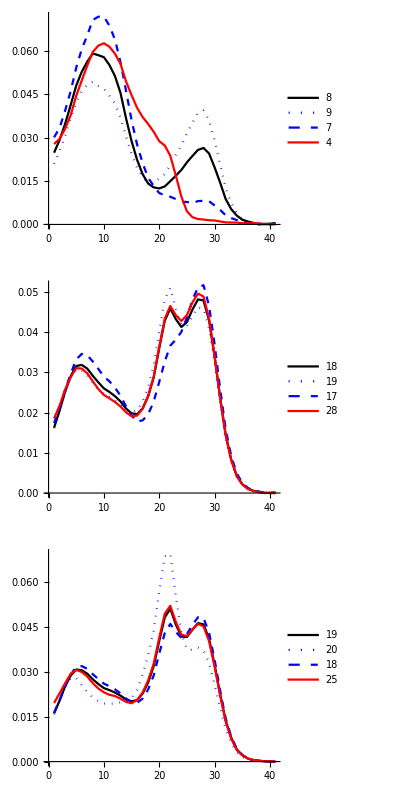

```mathematica
comparison[d_List,examine_List]:=ListLinePlot[
d[[examine,1]],
PlotLegends->Placed[examine,{Right,Top}],
PlotStyle->{Black,{Blue,Dotted},{Blue,Dashed},Red}]

GraphicsColumn[
comparison[normalizedData,#]&/@
{ {8,9,7,4}, {18,19,17,28}, {19,20,18,25} }]
```

Comment:  In the first case, this looks like a genuine problem with using the EMD metric—8 and 9 seem like they share the same type of peak structure.  But in the other two cases, it seems that the EMD matched spectra really are the closest, and the sources of error may be elsewhere.

## Next steps / Discussion

During the Noon meeting today, SM mentioned:

Need for better data—existing dataset was generated by a student pipetting by hand, and the pH meter readings may be off.

Campaign:  Use the robot to generate more examples in an effort to clean up the data.